## Page Rank

jeremykun.wordpress.com

```mathematica
rulesToPairs[i_->j_]:={i,j}; SetAttributes[rulesToPairs,Listable];

PageRank[graph_,p_]:= Module[{v,numVertices,prev,edgeRules,degrees,linkMatrixRules,linkMatrix},
edgeRules=EdgeRules[graph];
degrees=VertexOutDegree[graph];
numVertices = VertexCount[graph];

linkMatrixRules = Table[{pt⟦2⟧,pt⟦1⟧}->1/degrees⟦pt⟦1⟧⟧,{pt,rulesToPairs[edgeRules]}];
linkMatrix = SparseArray[linkMatrixRules,{numVertices,numVertices}];

v = Table[1.0,{numVertices}];
While[True,
prev = v;
v = (p/numVertices)+(1-p)Dot[linkMatrix,v];
v = v/Norm[v];
If[Norm[v-prev]<10^(-10),Break[]]
];
Return[Round[N[v],0.001]]
];
```

```mathematica
randomGraph[numVertices_,numEdges_] := RandomGraph[{numVertices,numEdges},DirectedEdges->True, VertexLabels->"Name",ImagePadding->10]
```

{0.056004,Null}

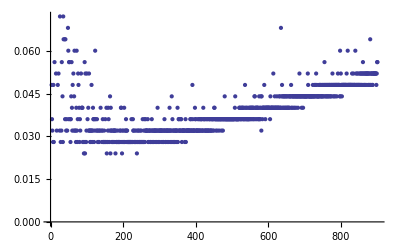

```mathematica
G =randomGraph[100,100];
Timing[PageRank[G,0.15];]
ListPlot[Table[Timing[PageRank[randomGraph[100,i],0.15]]⟦1⟧,{i,100,1000}]]
```

```mathematica
G = randomGraph[10,20];
visualizePageRanks[G_,p_]:=Module[{ranks},
ranks = PageRank[G,p];
Show[Graph[EdgeRules[G],VertexSize->Table[i->ranks⟦i⟧,{i,VertexCount[G]}],VertexLabels->"Name",ImagePadding->10]]
];
visualizePageRanks[G,0.25]
```